## Initial Conditions For Metric Perturbations From Master Scalars

## Using the master scalar formulation of 1909.04049, we can solve the massless wave equation for a “master scalar” that is gauge invariant. We then work backwards to the values of the metric perturbations, thereby providing initial data for Jecco nonlinear evolution

### 5D AdS black brane

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*z=1/r*)
X={t,z,x1,x2,x3};
```

```mathematica
d=5;
```

Since we know that the metric component  comprises the tensor sector master scalar (see JHEP 09 (2002) 043), we can include a scalar function at that position in the metric and determine its QNM spectrum
Note in the paper that  is the master scalar

```mathematica
G=1/z^2{{-f[z],-1,0,0,0},{-1, 0,0,0,0},{0,0,1,(2Pi T)^2 ϕ [t,z]/ 2,0},{0,0,(2Pi T)^2 ϕ[t,z] / 2,1, 0},{0,0,0,0,1}};
```

```mathematica
G//MatrixForm
```

(-f[z]/z^2 | -1/z^2 | 0 | 0 | 0
-1/z^2 | 0 | 0 | 0 | 0
0 | 0 | 1/z^2 | (2 π^2 T^2 ϕ[t,z])/z^2 | 0
0 | 0 | (2 π^2 T^2 ϕ[t,z])/z^2 | 1/z^2 | 0
0 | 0 | 0 | 0 | 1/z^2)

```mathematica
IG=Inverse[G];
```

```mathematica
Γ=Normal[Series[Table[1/2*Sum[IG[[i,l]]*(D[G[[j,l]],X[[k1]]]+D[G[[k1,l]],X[[j]]]-D[G[[j,k1]],X[[l]]]),{l,1,d}],{i,1,d},{j,1,d},{k1,1,d}],{ϵ,0,1}]];
```

```mathematica
Clear[Λ];
Λ = -(d-1)(d-2)/2;
```

```mathematica
Ric=Table[Sum[D[Γ[[k1,i,j]],X[[k1]]]-D[Γ[[k1,k1,i]],X[[j]]]+Sum[Γ[[q1,q1,k1]]Γ[[k1,i,j]]-Γ[[q1,i,k1]]Γ[[k1,q1,j]],{q1,1,d}],{k1,1,d}],{i,1,d},{j,1,d}];
R=Normal[Series[Sum[IG[[i,j]]Ric[[i,j]],{i,1,d},{j,1,d}],{ϵ,0,1}]];
```

```mathematica
Eing=Table[Ric[[i,j]]-1/2 R*G[[i,j]],{i,1,d},{j,1,d}];
```

```mathematica
(* Construct the Einstein Equations *)
EinEq=Simplify[Eing+ Λ G];
```

```mathematica
(* Module to linearize the equations *)
```

```mathematica
Linearize[eqn_, functions_,equilibrium_]:=
Module[{ϵ},
Normal@Series[eqn/.Thread[
functions->Map[Function[{t,z},#]&,
equilibrium + ϵ Through[
Thread[δ[functions]][t,z]]]],{ϵ,0,1}]/.ϵ->1
]
```

```mathematica
(* Linearize the Einstein equations. Background solution is black brane with ϕ0 = 0 *)
```

```mathematica
LinearEinsteins = With[{
eqn = EinEq/.{f->Function[z,1-z^4/zh^4]/.T->1/(Pi zh)} //Simplify,
functions={ϕ},
equilibrium = {0} },
Linearize[eqn, functions, equilibrium]
]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,(π^2 T^2 ((z^4+3 zh^4) δ[ϕ]^(0,1)[t,z]+(z^5-z zh^4) δ[ϕ]^(0,2)[t,z]+zh^4 (-3 δ[ϕ]^(1,0)[t,z]+2 z δ[ϕ]^(1,1)[t,z])))/(z zh^4),0},{0,0,(π^2 T^2 ((z^4+3 zh^4) δ[ϕ]^(0,1)[t,z]+(z^5-z zh^4) δ[ϕ]^(0,2)[t,z]+zh^4 (-3 δ[ϕ]^(1,0)[t,z]+2 z δ[ϕ]^(1,1)[t,z])))/(z zh^4),0,0},{0,0,0,0,0}}

### Solving the equation

```mathematica
(*the ingoing coordinate v=(t- Integrate[1/f[z],z])*)
exponential=Exp[-ⅈ ω t(*(t- Integrate[1/f[z],z])*)];
```

```mathematica
eqn = DeleteDuplicates@Flatten@LinearEinsteins/.δ[ϕ]->Thread[ϕ,{t,z}]/.T->1/(Pi zh)//FullSimplify
```

{0,((z^4+3 zh^4) ϕ^(0,1)[t,z]+(z^5-z zh^4) ϕ^(0,2)[t,z]+zh^4 (-3 ϕ^(1,0)[t,z]+2 z ϕ^(1,1)[t,z]))/(z zh^6)}

```mathematica
eqn = %[[2]]/.ϕ->Function[{t,z},ϕ[z]Exp[-ⅈ ω (t)]]/.f->Function[z,1-z^4/zh^4]//FullSimplify
```

(ⅇ^(-ⅈ t ω) (3 ⅈ zh^4 ω ϕ[z]+(z^4+3 zh^4-2 ⅈ z zh^4 ω) ϕ'[z]+z (z^4-zh^4) ϕ''[z]))/(z zh^6)

```mathematica
eqn =  (3 ⅈ zh^4 ω ϕ[z]+(z^4+3 zh^4-2 ⅈ z zh^4 ω) ϕ'[z]+z (z^4-zh^4) ϕ''[z])
```

3 ⅈ zh^4 ω ϕ[z]+(z^4+3 zh^4-2 ⅈ z zh^4 ω) ϕ'[z]+z (z^4-zh^4) ϕ''[z]

Note that the scalar field equation  yields
eqn=Sum[1/(√(-Det[G]))D[√(-Det[G]) IG[[k,l]]D[ϕ[z]exponential,X[[l]]],X[[k]]],{k,1,d},{l,1,d}]/.f->Function[z,1-z^4/zh^4]//FullSimplify 
eqn= (3 ⅈ zh^4 ω ϕ[z]+(z^4+3 zh^4-2 ⅈ z zh^4 ω) ϕ'[z]+z (z^4-zh^4) ϕ''[z]);
As expected.

```mathematica
(*scaling dimension: Δ=0 or Δ=4*)
(*It means that the source appears at order 0 and the vev at order 4.*)
```

```mathematica
Normal[Series[eqn/.ω->0/.zh->1/.ϕ->Function[z, z^Δ],{z,0,1}]]//Factor
```

-z^(-2+Δ) (-4+Δ) Δ

```mathematica
(* because the end points of our domain[0,1] are regular singular points, we need to impose boundary conditions slightly away from there. Because of this, we need to solve the equations analytically order by order close to the z=0 and close to z=1 in a perturbative way.*)
```

#### AdS Boundary Expansion

```mathematica
(*Since we want the source to be zero, the expansion starts at order d-1, i.e. ϕ= vev z^(d-1)+... *)
(* Expand around z=0 in a power series then equate powers of z. Express in terms of unknown constant of leading order *)
```

```mathematica
Clear[acoeffs];
acoeffs={a4,a5,a6,a7,a8,a9,a10,a11,a12, a13,a14};
Expansion = eqn/.ϕ->Function[z,Sum[acoeffs[[i+1]]z^(i+(d-1)),{i,0,Length[acoeffs]-1}]]//FullSimplify//Collect[#,z]&
```

144 a12 z^15+169 a13 z^16+196 a14 z^17+z^10 (49 a7-77 a11 zh^4-17 ⅈ a10 zh^4 ω)+z^11 (64 a8-96 a12 zh^4-19 ⅈ a11 zh^4 ω)+z^12 (81 a9-117 a13 zh^4-21 ⅈ a12 zh^4 ω)+z^13 (100 a10-140 a14 zh^4-23 ⅈ a13 zh^4 ω)+z^14 (121 a11-25 ⅈ a14 zh^4 ω)+z^4 (-5 a5 zh^4-5 ⅈ a4 zh^4 ω)+z^5 (-12 a6 zh^4-7 ⅈ a5 zh^4 ω)+z^6 (-21 a7 zh^4-9 ⅈ a6 zh^4 ω)+z^7 (16 a4-32 a8 zh^4-11 ⅈ a7 zh^4 ω)+z^8 (25 a5-45 a9 zh^4-13 ⅈ a8 zh^4 ω)+z^9 (36 a6-60 a10 zh^4-15 ⅈ a9 zh^4 ω)

```mathematica
(* Solving loop: start a list with the non-zero constant*)
(* Starting at n=4, extract the highest power, solve for the coefficient in terms of a3, then add to the list *)
```

```mathematica
a={};
For[n=d-1,n<=Length[acoeffs]+2,n++,
expr =Normal[Series[Expansion,{z,0,n}]]-Normal[Series[Expansion,{z,0,n-1}]];
Print[expr];
If[n==d-1,Solve[expr==0,acoeffs[[n-(d-1)+2]]]//FullSimplify//AppendTo[a,#[[1]][[1]]]&,
Solve[expr==0/.Dispatch[a],acoeffs[[n-(d-1)+2]]]//FullSimplify//AppendTo[a,#[[1]][[1]]]&]]
a
```

z^4 (-5 a5 zh^4-5 ⅈ a4 zh^4 ω)

z^5 (-12 a6 zh^4-7 ⅈ a5 zh^4 ω)

z^6 (-21 a7 zh^4-9 ⅈ a6 zh^4 ω)

z^7 (16 a4-32 a8 zh^4-11 ⅈ a7 zh^4 ω)

z^8 (25 a5-45 a9 zh^4-13 ⅈ a8 zh^4 ω)

z^9 (36 a6-60 a10 zh^4-15 ⅈ a9 zh^4 ω)

z^10 (49 a7-77 a11 zh^4-17 ⅈ a10 zh^4 ω)

z^11 (64 a8-96 a12 zh^4-19 ⅈ a11 zh^4 ω)

z^12 (81 a9-117 a13 zh^4-21 ⅈ a12 zh^4 ω)

z^13 (100 a10-140 a14 zh^4-23 ⅈ a13 zh^4 ω)

{a5→-ⅈ a4 ω,a6→-(7 a4 ω^2)/12,a7→1/4 ⅈ a4 ω^3,a8→a4 (1/(2 zh^4)+(11 ω^4)/128),a9→-(ⅈ a4 ω (4032/zh^4+143 ω^4))/5760,a10→a4 (-(21 ω^2)/(40 zh^4)-(143 ω^6)/23040),a11→(ⅈ a4 ω^3 (44352/zh^4+221 ω^4))/161280,a12→a4 (1/(3 zh^8)+(143 ω^4)/(1280 zh^4)+(4199 ω^8)/15482880),a13→-(ⅈ a4 ω (3612672+247104 zh^4 ω^4+323 zh^8 ω^8))/(6635520 zh^8),a14→-(a4 ω^2 (431456256+9801792 zh^4 ω^4+7429 zh^8 ω^8))/(928972800 zh^8)}

```mathematica
(* Use these coefficients and check that the equation is zero up to the maximal order *)
```

```mathematica
Normal[Series[eqn /.ϕ->Function[z, Sum[acoeffs[[i]]z^(i+3),{i,1,Length[acoeffs]}]] /.Dispatch[a]//Simplify,{z,0,13}]]
```

0

## Near-horizon Expansion

```mathematica
(* Now do the same thing around z=Subscript[z, h]. Do do so, expand the coefficients of the scalar terms in a Taylor series around z=Subscript[z, h]
and then substitute the expansion for ϕ *)
```

```mathematica
Clear[bcoeffs];
bcoeffs={b1,b2,b3,b4,b5,b6};
NHExpansion=Series[eqn/.ϕ->Function[z,(*(z-zh)*)(b0 + Sum[bcoeffs[[j]] (z-zh)^j, {j,1,Length[bcoeffs]}])],{z,zh,6}]//Collect[#,z-1]&
```

(4 b1 zh^4+3 ⅈ b0 zh^4 ω-2 ⅈ b1 zh^5 ω)+(4 b1 zh^3+16 b2 zh^4+ⅈ b1 zh^4 ω-4 ⅈ b2 zh^5 ω) (z-zh)+(6 b1 zh^2+28 b2 zh^3+36 b3 zh^4-ⅈ b2 zh^4 ω-6 ⅈ b3 zh^5 ω) (z-zh)^2+(4 b1 zh+12 b2 zh^2+4 (5 b2 zh^2+15 b3 zh^3+12 b4 zh^4)+3 ⅈ b3 zh^4 ω+3 b3 (4 zh^3-2 ⅈ zh^4 ω)+4 b4 (4 zh^4-2 ⅈ zh^5 ω)) (z-zh)^3+(b1+8 b2 zh+18 b3 zh^2+10 (b2 zh+6 b3 zh^2+12 b4 zh^3+8 b5 zh^4)+3 ⅈ b4 zh^4 ω+4 b4 (4 zh^3-2 ⅈ zh^4 ω)+5 b5 (4 zh^4-2 ⅈ zh^5 ω)) (z-zh)^4+(2 b2+12 b3 zh+24 b4 zh^2+2 (b2+15 b3 zh+60 b4 zh^2+100 b5 zh^3+60 b6 zh^4)+3 ⅈ b5 zh^4 ω+5 b5 (4 zh^3-2 ⅈ zh^4 ω)+6 b6 (4 zh^4-2 ⅈ zh^5 ω)) (z-zh)^5+(3 b3+16 b4 zh+30 b5 zh^2+2 (3 b3+30 b4 zh+100 b5 zh^2+150 b6 zh^3)+3 ⅈ b6 zh^4 ω+6 b6 (4 zh^3-2 ⅈ zh^4 ω)) (z-zh)^6+O[z-zh]^7

```mathematica
ClearAll[n]
```

```mathematica
(* Starting at n=0, extract the highest power of (z-Subscript[z, h]), solve for the coefficient in terms of b0, then add to the list *)
b={};
For[n=0,n<Length[bcoeffs],n++,
expr =Normal[Series[NHExpansion,{z,zh,n}]]-Normal[Series[NHExpansion,{z,zh,n-1}]]//FullSimplify;
Print[expr];
If[n==0,AppendTo[b,Solve[expr ==0, bcoeffs[[n+1]]][[1]][[1]]//FullSimplify],AppendTo[b,Solve[expr==0/.Dispatch[b],bcoeffs[[n+1]]][[1]][[1]]//FullSimplify]]];
b
```

zh^4 (3 ⅈ b0 ω+b1 (4-2 ⅈ zh ω))

(z-zh) zh^3 (4 b1+16 b2 zh+ⅈ zh (b1-4 b2 zh) ω)

(z-zh)^2 zh^2 (6 b1+zh (28 b2+36 b3 zh-ⅈ zh (b2+6 b3 zh) ω))

(z-zh)^3 zh (4 b1+zh (32 b2+zh (72 b3+64 b4 zh-ⅈ zh (3 b3+8 b4 zh) ω)))

(z-zh)^4 (b1+2 zh (9 b2+zh (39 b3+68 b4 zh+50 b5 zh^2))-5 ⅈ zh^4 (b4+2 b5 zh) ω)

(z-zh)^5 (4 b2+zh (42 b3+4 zh (36 b4+55 b5 zh+36 b6 zh^2)-ⅈ zh^3 (7 b5+12 b6 zh) ω))

{b1→(3 b0 ω)/(4 ⅈ+2 zh ω),b2→(3 b0 ω (-4 ⅈ+zh ω))/(8 zh (-8+6 ⅈ zh ω+zh^2 ω^2)),b3→-(b0 ω (16+zh ω (48 ⅈ+zh ω)))/(16 zh^2 (2 ⅈ+zh ω) (4 ⅈ+zh ω) (6 ⅈ+zh ω)),b4→(3 b0 ω (-384 ⅈ+zh ω (-688+zh ω (-24 ⅈ+zh ω))))/(128 zh^3 (2 ⅈ+zh ω) (4 ⅈ+zh ω) (6 ⅈ+zh ω) (8 ⅈ+zh ω)),b5→-(3 b0 ω (35840+zh ω (-23296 ⅈ+5 zh ω (1488+zh ω (32 ⅈ+zh ω)))))/(1280 zh^4 (2 ⅈ+zh ω) (4 ⅈ+zh ω) (6 ⅈ+zh ω) (8 ⅈ+zh ω) (10 ⅈ+zh ω)),b6→(7 b0 ω (307200 ⅈ+zh ω (-133120+zh ω (162624 ⅈ+5 zh ω (-1840+zh ω (36 ⅈ+zh ω))))))/(5120 zh^5 (2 ⅈ+zh ω) (4 ⅈ+zh ω) (6 ⅈ+zh ω) (8 ⅈ+zh ω) (10 ⅈ+zh ω) (12 ⅈ+zh ω))}

```mathematica
(* As before, check that this is solved up to highest order in (z-1) *)
```

```mathematica
Normal[Series[eqn/.ϕ->Function[z,(b0 + Sum[bcoeffs[[i]](z-zh)^i,{i,1,Length[bcoeffs]}])/.Dispatch[b]]//Simplify,{z,zh,0}]]//Simplify
```

0

### Shooting Method -- Specify z_h

```mathematica
Subscript[z, h]=1;
```

```mathematica
(*Better to redefine ϕ to extract a factor of z^(d-1)-- easier implementation of BC at z=0. This is an optional step*)
z^(1-d) eqn/. ϕ->Function[z, z^(d-1)ϕ[z]]/.zh->Subscript[z, h]//Simplify
```

(16 z^3-5 ⅈ ω) ϕ[z]+(-5+9 z^4-2 ⅈ z ω) ϕ'[z]+z (-1+z^4) ϕ''[z]

```mathematica
eqnlist[ω_]:={((16 z^3+5 ⅈ ω) ϕ[z]+(-5+9 z^4+2 ⅈ z ω) ϕ'[z]+z (-1+z^4) ϕ''[z])};
```

```mathematica
(* Near-horizon scalar field from determined coefficients *)
z^(1-d)(b0 + Sum[bcoeffs[[i]] (z-zh)^i,{i,1,Length[bcoeffs]}]/.Dispatch[b]/.b0->ϕ0)/.zh->Subscript[z, h]//Collect[#,(z-Subscript[z, h])]&//Simplify
```

1/(5120 z^4)ϕ0 (5120+(7680 (-1+z) ω)/(2 ⅈ+ω)+(1920 (-1+z)^2 ω (-4 ⅈ+ω))/(-8+6 ⅈ ω+ω^2)-(320 (-1+z)^3 ω (16+ω (48 ⅈ+ω)))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω))+(120 (-1+z)^4 ω (-384 ⅈ+ω (-688+ω (-24 ⅈ+ω))))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω) (8 ⅈ+ω))-(12 (-1+z)^5 ω (35840+ω (-23296 ⅈ+5 ω (1488+ω (32 ⅈ+ω)))))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω) (8 ⅈ+ω) (10 ⅈ+ω))+(7 (-1+z)^6 ω (307200 ⅈ+ω (-133120+ω (162624 ⅈ+5 ω (-1840+ω (36 ⅈ+ω))))))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω) (8 ⅈ+ω) (10 ⅈ+ω) (12 ⅈ+ω)))

```mathematica
(* Need to copy and paste the expression above into the function definition *)
NHϕ[ϕ0_, ω_][z_]:=(5120+(7680 (-1+z) ω)/(2 ⅈ+ω)+(1920 (-1+z)^2 ω (-4 ⅈ+ω))/(-8+6 ⅈ ω+ω^2)-(320 (-1+z)^3 ω (16+ω (48 ⅈ+ω)))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω))+(120 (-1+z)^4 ω (-384 ⅈ+ω (-688+ω (-24 ⅈ+ω))))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω) (8 ⅈ+ω))-(12 (-1+z)^5 ω (35840+ω (-23296 ⅈ+5 ω (1488+ω (32 ⅈ+ω)))))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω) (8 ⅈ+ω) (10 ⅈ+ω))+(7 (-1+z)^6 ω (307200 ⅈ+ω (-133120+ω (162624 ⅈ+5 ω (-1840+ω (36 ⅈ+ω))))))/((2 ⅈ+ω) (4 ⅈ+ω) (6 ⅈ+ω) (8 ⅈ+ω) (10 ⅈ+ω) (12 ⅈ+ω)));
```

```mathematica
(* Near-boundary scalar field from determined coefficients *)
Sum[acoeffs[[i]] z^(i-1),{i,1,Length[acoeffs]}]/.Dispatch[a]/.a4->ϕvev/.zh->Subscript[z, h]//Collect[#,z]&
```

ϕvev-ⅈ z ϕvev ω-7/12 z^2 ϕvev ω^2+1/4 ⅈ z^3 ϕvev ω^3+z^4 ϕvev (1/2+(11 ω^4)/128)-(ⅈ z^5 ϕvev ω (4032+143 ω^4))/5760+(ⅈ z^7 ϕvev ω^3 (44352+221 ω^4))/161280+z^6 ϕvev (-(21 ω^2)/40-(143 ω^6)/23040)+z^8 ϕvev (1/3+(143 ω^4)/1280+(4199 ω^8)/15482880)-(ⅈ z^9 ϕvev ω (3612672+247104 ω^4+323 ω^8))/6635520-(z^10 ϕvev ω^2 (431456256+9801792 ω^4+7429 ω^8))/928972800

```mathematica
(* Need to copy and paste the expression above into the function definition *)
Asϕ[ϕvev_, ω_][z_]:=ϕvev-ⅈ z ϕvev ω-7/12 z^2 ϕvev ω^2+1/4 ⅈ z^3 ϕvev ω^3+z^4 ϕvev (1/2+(11 ω^4)/128)-(ⅈ z^5 ϕvev ω (4032+143 ω^4))/5760+(ⅈ z^7 ϕvev ω^3 (44352+221 ω^4))/161280+z^6 ϕvev (-(21 ω^2)/40-(143 ω^6)/23040)+z^8 ϕvev (1/3+(143 ω^4)/1280+(4199 ω^8)/15482880)-(ⅈ z^9 ϕvev ω (3612672+247104 ω^4+323 ω^8))/6635520-(z^10 ϕvev ω^2 (431456256+9801792 ω^4+7429 ω^8))/928972800;
```

```mathematica
(*Integration from z=0 to the middle*)
F2[ϕvev_?NumberQ,ω_?NumberQ,bound_?NumberQ]:={ϕ[bound],ϕ'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω][[i]]==0,{i,1,1}],ϕ[small]==Asϕ[ϕvev,ω][small],
ϕ'[small]==Asϕ[ϕvev,ω]'[small]}],{ϕ},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]

ASY[ϕvev_?NumberQ,ω_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω][[i]]==0,{i,1,1}],ϕ[small]==Asϕ[ϕvev,ω][small],
ϕ'[small]==Asϕ[ϕvev,ω]'[small]}],{ϕ},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
(*Integration from middle to z=1*)F1[ϕ0_?NumberQ,ω_?NumberQ,bound_?NumberQ]:={ϕ[bound],ϕ'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω][[i]]==0,{i,1,1}],ϕ[ 1-smallIR]==NHϕ[ϕ0,ω][ 1-smallIR],ϕ'[ 1-smallIR]==NHϕ[ϕ0,ω]'[ 1-smallIR]}],{ϕ},{z,bound, 1-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]

NH[ϕ0_?NumberQ,ω_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω][[i]]==0,{i,1,1}],ϕ[ 1-smallIR]==NHϕ[ϕ0,ω][ 1-smallIR],ϕ'[ 1-smallIR]==NHϕ[ϕ0,ω]'[ 1-smallIR]}],{ϕ},{z,bound, 1-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
(*Newton-Raphson method: at every step it changes the value of ϕvev and ω (starting from an initial guess that we give) until the integration from the left and the integration from the right give the same value for the field and its derivative in the middle: ϕ[bound], ϕ'[bound]*)
Clear[GG];
GG[midd_]:=FindRoot[F2[ϕvev,ω,midd]==F1[1,ω,midd],{ϕvev,Tϕvev},{ω,Tω},WorkingPrecision->wp,StepMonitor:>Print[F2[ϕvev,ω,midd]-F1[1,ω,midd]]];
```

```mathematica
smallIR=10^-8;
small=10^-6;
bound =5/10;
wp=55;
```

```mathematica
{Tϕvev,Tω}={1+I,4+4I};
```

```mathematica
GG[bound]//Quiet
```

{-0.49089600885985588838731078075170632208862526252962+1.7711212850423802059783639797087603829676986371625582 ⅈ,1.40041738763221472911715926466564111751177041926499-7.614281836922548120437904370709717999624736644918762 ⅈ}

{-0.3509787987668593264932681703526956142602927965670552+0.37726834796872177266290467592289737576567982283348347 ⅈ,1.24080326718475332007076729588068066447722263523739-1.23446870807021852929849896596377102904863591288358 ⅈ}

{-0.2783829879196163561930429081236072608347552296941677+0.30345340838874709937033246063128877499451963255036407 ⅈ,0.937078033257090391146125969688805533709318537407073-1.06445182923924550410922642676872260202053742063363 ⅈ}

{-0.0214278863548109146001904886004597952878381785930176-0.00981655072030567875950328577889861362799293047750032 ⅈ,0.079670909968528935956658333017055621395266248266148-0.373759104380356463622254385088969024210783670930475 ⅈ}

{-0.0033579508908124400489128513212527588393570347427647+0.00362119552761708050577303888792259333998481832150453 ⅈ,0.01465665153209492018641132104854093789710639526617-0.05432559639560626447797363795597771236054280362904 ⅈ}

{-0.00005210663169246377426658250114914987573216773169402+0.00004409496417002101730016710222243456170032725108536 ⅈ,0.00036529286913940863820463653918057403637415900075-0.000566675034872234301945230331821313418189218558677 ⅈ}

{-8.14397126435310755791023918512593541205814146×10^-9-1.88319880835690963001615655430627574412259×10^-10 ⅈ,7.7186385486525491613299398181560004163892953×10^-8-1.507604473772917951111933357492576409186261×10^-8 ⅈ}

{1.47463814318275893207128884421329737×10^-17-1.039352312130354095693556040213535129×10^-16 ⅈ,3.910739432179927175606830935781459×10^-17+1.02386854211862682021315097626159895×10^-15 ⅈ}

{-1.8007568707928712083×10^-32+1.60184475696674750276×10^-32 ⅈ,2.049972514952817152×10^-31-2.7254341122592815529×10^-31 ⅈ}

{7.2848×10^-48-2.366×10^-49 ⅈ,-1.1331×10^-46+8.0186×10^-47 ⅈ}

{ϕvev→-15.7950376284496370506003437665342337933468389339873555-44.79878666483584274844113211475529649918343553542271477 ⅈ,ω→5.169520975762229549404618858179431425719971970164016097+4.763570116920460863645146483965946597446088357461202615 ⅈ}

```mathematica
{ϕvev->-15.79580470746918506167762437545892886598578928681675345739739029102729451071179`55.-44.79911603541786660966127959632532578392261857116266206520565343741672285605689`55. ⅈ,ω->-5.16952097576222954940461885889722499194572185535488411636773071714438971882811`55.-4.76357011692046086364514648370905218950138549522150190381951475957642922361821`55. ⅈ}
```

{ϕvev→-15.79580470746918506167762437545892886598578928681675346-44.79911603541786660966127959632532578392261857116266207 ⅈ,ω→-5.169520975762229549404618858897224991945721855354884116-4.763570116920460863645146483709052189501385495221501904 ⅈ}

```mathematica
sl
```

{ϕ→InterpolatingFunction[…]}

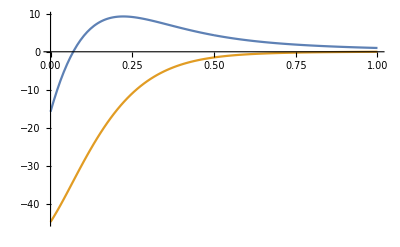

```mathematica
result=%;
sl=NH[1,ω,bound]/.result//Quiet;
sl1=ASY[ϕvev,ω,bound]/.result//Quiet;
Show[Plot[{ϕ[z]/.sl1//Re,ϕ[z]/.sl1//Im},{z,0,bound},PlotRange->All],Plot[{ϕ[z]/.sl//Re,ϕ[z]/.sl//Im},{z,bound,zh},PlotRange->All],PlotRange->All]/.zh->Subscript[z, h]//Quiet
```

### Construct radial profile

```mathematica
(* Take the two piecewise solutions and stitch them together into a single interpolating function*)
```

```mathematica
Φ=Function[z,Piecewise[{{ϕ[z]/.sl1,0<=z<=bound},{ϕ[z]/.sl,bound<=z<=zh}}]]/.zh->Subscript[z, h]
```

Function[z,Piecewise[{{ϕ[z]/.sl1, 0≤z≤bound}, {ϕ[z]/.sl, bound≤z≤1}}]]

```mathematica
ϕInterp = Interpolation[Table[{z,Evaluate[Φ[z]]},{z,0,zh,10^-4}]]/.zh->Subscript[z, h]//Quiet
```

InterpolatingFunction[{{0, 1.00000000000000000000000000000000000000}}, <>]

```mathematica
(* In terms of the metric perturbation *)
```

```mathematica
hMet[z_]= zh^2 z^2 ϕInterp[z]/.zh->Subscript[z, h]
```

z^2 InterpolatingFunction[{{0, 1.00000000000000000000000000000000000000}}, <>][z]

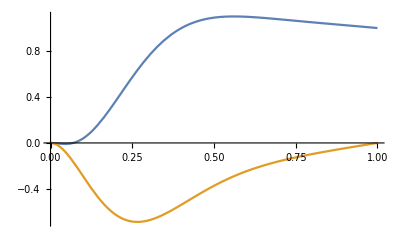

```mathematica
Plot[{hMet[z]//Re,hMet[z]//Im},{z,0,zh}/.zh->Subscript[z, h],PlotRange->All]
```

### Export

```mathematica
(* Rescale by the maximum real value reached by the field. *)
```

```mathematica
(* Initial metric perturbation *)
```

```mathematica
A=1;
```

0.908411 z^2 InterpolatingFunction[{{0, 1.00000000000000000000000000000000000000}}, <>][z]

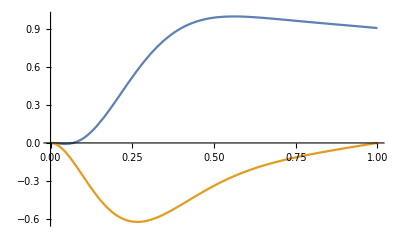

```mathematica
hOut[z_]=A hMet[z]/FindMaxValue[{Re[hMet[z]],0<=z<=zh}/.zh->Subscript[z, h],z]
Plot[{hOut[z]//Re,hOut[z]//Im},{z,0,zh}/.zh->Subscript[z, h],PlotRange->All]
```

```mathematica
(* First overtone frequency *)
ω/.result[[2]]
```

-5.169520975762229549404618858897224991945721855354884116-4.763570116920460863645146483709052189501385495221501904 ⅈ

### Calculate the energy contained in the QNM

#### Recall that the energy for a scalar field in Ingoing Eddington-Finklestein coordinates on an AdS_5 black brane is where is the tortoise coordinate is related to the compactified radial coordinate by Therefore, for a massless scalar field the energy is written as Recall that the master scalar in the tensor channel is . Substituting this into gives the energy for the metric perturbation

```mathematica
(* Calculate the energy in the normalized metric peturbation *)
```

```mathematica
Integrand[z_]=(1-z^4)(4 z^2 (Abs[hOut[z]])^2 +4 z^3 Abs[hOut[z]] Abs[Derivative[1][hOut][z]]+ z^4 (Abs[Derivative[1][hOut][z]])^2 )/.result[[2]];
Energy=NIntegrate[(1/2) Integrand[z],{z,0,1}]
```

0.608646

```mathematica
Energy//FullForm
```

0.608646

```mathematica
Solve[0.001521614148370852==0.60864565934834 n]
```

{}

```mathematica
1/400//N
```

0.0025

```mathematica
0.6086456593483407^8
```

0.0188329